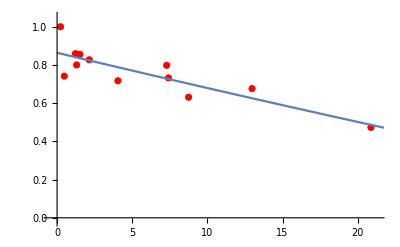

```mathematica
data={{1.52,0.855},{7.41,0.732},{2.14,0.827},{8.75,0.631},{12.97,0.676},{0.48,0.741},{7.29,0.798},{0.23,1.0},{1.22,0.859},{4.05,0.717},{20.88,0.473},{1.3,0.800}};
fit=Fit[data,{1,x,x^2}, x];
Show[ListPlot[data, PlotStyle->Red], Plot[fit, {x, 0, 30}]]
```

```mathematica
fit[11]
```

(0.863585-0.0188024 x+0.0000356212 x^2)[11]